```mathematica
(*Setting options for figure plotting*)
```

```mathematica
th = 0.005;fs=16;
SetOptions[Plot, LabelStyle->Directive[FontFamily->"Myriad Pro", Black, FontSize->fs], PlotStyle-> {Blue,Thickness[th]}, PlotRange->All];
SetOptions[ListPlot, LabelStyle->Directive[FontFamily->"Myriad Pro", Black, FontSize->fs], PlotStyle-> {Blue,PointSize[th]}, PlotRange->All];
SetOptions[ListLogPlot, LabelStyle->Directive[FontFamily->"Myriad Pro", Black, FontSize->fs], PlotStyle-> {Blue,PointSize[th]}, PlotRange->All];
SetOptions[ListLinePlot, LabelStyle->Directive[FontFamily->"Myriad Pro", Black, FontSize->fs], PlotStyle-> {Blue,Thickness[th]}, PlotRange->All];
SetOptions[ParametricPlot, LabelStyle->Directive[FontFamily->"Myriad Pro", Black, FontSize->fs], PlotStyle-> {Blue,Thickness[th]}, PlotRange->All];
SetOptions[ListPointPlot3D, LabelStyle->Directive[FontFamily->"Myriad Pro", Black, FontSize->fs], PlotStyle-> {Blue,Thickness[th]}, PlotRange->All];
SetOptions[MatrixPlot, BaseStyle->Directive[FontFamily->"Myriad Pro", Black, FontSize->fs]];
SetOptions[BoxWhiskerChart, BaseStyle->Directive[FontFamily->"Myriad Pro", Black,Bold, FontSize->fs]];
SetOptions[DistributionChart, BaseStyle->Directive[FontFamily->"Myriad Pro", Black,Bold, FontSize->fs]];
```

```mathematica
(*exctract the full gut vertices and convert it to .csv*)
```

```mathematica
ClearAll["Global`*"]

experimentIndx =5;

rawControlFileDir= FileNameJoin[{NotebookDirectory[] , "Experiment" <> ToString[experimentIndx], "Control-centerlines"}];

rawTreatmentFileDir= FileNameJoin[{NotebookDirectory[] , "Experiment" <> ToString[experimentIndx], "Treatment-centerlines"}];


positionDirectory = FileNameJoin[{NotebookDirectory[], "Smoothed centerlines"}];

(*SetDirectory[rawFileDir];*)


convertThenExport[rawDir_][fileName_]:=(
SetDirectory[rawDir];
data = ToExpression@StringSplit[(Import[fileName, "Data"][[7;;]])//Flatten];

points =  data[[;;;;4, 3;;5]];



smooth= 0.3;
newPoints = {LowpassFilter[points[[;;,1]],smooth],LowpassFilter[points[[;;,2]],smooth],-LowpassFilter[points[[;;,3]],smooth]}//Transpose;

SetDirectory[positionDirectory];


outName = StringReplace[fileName, ".swc" -> ".csv"];
Export[outName, newPoints]
)

SetDirectory[rawControlFileDir];
fileNames = FileNames[];
convertThenExport[rawControlFileDir] /@ fileNames;


SetDirectory[rawTreatmentFileDir];
fileNames = FileNames[];
convertThenExport[rawTreatmentFileDir] /@ fileNames;
```

```mathematica
(*get the the midgut part*)
```

```mathematica
ClearAll["Global`*"]

experimentIndx =5;

experimentDir= FileNameJoin[{NotebookDirectory[] , "Experiment" <> ToString[experimentIndx]}];

rawControlFileDir= FileNameJoin[{experimentDir, "Control-centerlines"}];

rawTreatmentFileDir= FileNameJoin[{experimentDir, "Treatment-centerlines"}];


positionDirectory = FileNameJoin[{NotebookDirectory[], "Smoothed centerlines-cut"}];



SetDirectory[experimentDir];
excelSheet = Import[FileNames["*.csv"][[1]]];
excelNames = excelSheet[[2;;,1]];
excelNames = StringDelete[excelNames,".traces"];

landmarks1 = excelSheet[[2;;, {4,5,6}]];
landmarks2 = excelSheet[[2;;, {8,9,10}]];


plotCenterlineLandmarks[rawDir_][fileIndex_]:=(
SetDirectory[rawDir];
fileNames = FileNames[];
fileName = fileNames[[fileIndex]];


data = ToExpression@StringSplit[(Import[fileName, "Data"][[7;;]])//Flatten];



points = data[[;;;;4, 3;;5]];


 inds = Position[StringContainsQ[fileName,#]&/@excelNames, True]//Flatten;
nameIndex = inds[[Ordering[StringLength[excelNames[[inds]]],-1][[1]]]];


(*{fileIndex, fileName, excelNames[[nameIndex]]}*)

lndmrkPos1 = landmarks1[[nameIndex]];
lndmrkPos2 =  landmarks2[[nameIndex]];

landMarkIndex1 = Nearest[points->"Index", lndmrkPos1][[1]];
landMarkIndex2 = Nearest[points->"Index", lndmrkPos2][[1]];

cutPoints = points[[Min[landMarkIndex1, landMarkIndex2];;Max[landMarkIndex1, landMarkIndex2]]];

smooth= 0.3;
newPoints ={ LowpassFilter[cutPoints[[;;, 1]], smooth], LowpassFilter[cutPoints[[;;, 2]], smooth], -LowpassFilter[cutPoints[[;;, 3]], smooth] }//Transpose;

SetDirectory[positionDirectory];
outName =StringReplace[fileName, ".swc" -> ".csv"];
Export[outName, newPoints]

)

SetDirectory[rawControlFileDir];
fileNames1 = FileNames[]; numFiles1 = Length[fileNames1];
plotCenterlineLandmarks[rawControlFileDir] /@ Range[numFiles1];



SetDirectory[rawTreatmentFileDir];
fileNames2 = FileNames[]; numFiles2= Length[fileNames2];
plotCenterlineLandmarks[rawTreatmentFileDir] /@ Range[numFiles2];
```

```mathematica
(*Show Curves and results*)
```

```mathematica
ClearAll["Global`*"]
positionDirectory = FileNameJoin[{NotebookDirectory[], "Smoothed centerlines-cut"}];
fitDirectory = FileNameJoin[{NotebookDirectory[], "FitResults-cut"}];
resultDirectory =FileNameJoin[{NotebookDirectory[], "RunResults"}];

figureDir = FileNameJoin[{ParentDirectory[NotebookDirectory[],2], "For the paper", "Figures"}];



SetDirectory[positionDirectory];

fileNames = StringTake[FileNames[], {1, -5}];

numFiles = Length[fileNames];

cc = -1; smoothing = 0.2;


changeDirectories[cutIndx_]:= (

cutName = {"", "-cut"}[[cutIndx]];

positionDirectory = FileNameJoin[{NotebookDirectory[],  "Smoothed centerlines" <> cutName}];
fitDirectory = FileNameJoin[{NotebookDirectory[],  "FitResults" <> cutName}];

)


getVerts[index_]:= (
SetDirectory[positionDirectory];
name = fileNames[[index]];
verts = Import[name <>".csv"];
(*indMax = Ordering[verts[[;;,3]],-1][[1]];

Transpose[Transpose[verts] - verts[[indMax]]]*)

Transpose[Transpose[verts] - verts[[1]]]

)

tracePlot[nArcS_:0][index_] := (
	SetDirectory[fitDirectory];
	name = fileNames[[index]];

	arcLengths = Import[name <> "-arcLengths.csv"]//Flatten;
	nArcLengths = (arcLengths - Min[arcLengths])/(Max[arcLengths] - Min[arcLengths]);
	
	colors = ColorData["AvocadoColors"]/@ nArcLengths;

	verts= getVerts[index];
 

	indP = Nearest[nArcLengths->"Index", nArcS][[1]];

	point[ind_] := {colors[[ind]], Point[verts[[ind]]]};
	points = point /@ Range[colors//Length];
	Graphics3D[{PointSize[0.015],points, Red, Opacity[0.5], PointSize[0.05], Point[verts[[indP]]]}, Axes->True, LabelStyle->Directive[Bold, FontSize-> 18, Black], AxesLabel->{x,y,z}]
)


centeredPoints2D[index_]:= (

	name = fileNames[[index]];
	
	SetDirectory[positionDirectory];
	verts = Import[name <>".csv"]; verts[[;;,3]] -= Max[ verts[[;;,3]]];

	verts = Transpose[Transpose[verts] - Mean[verts]];

	majorAxis =  Eigenvectors[Covariance[verts]][[1]];
	majorAxis  *= Sign[majorAxis[[3]] ];


	rMat = RotationMatrix[{{0,0,1},majorAxis}];


	(*covMat = Eigenvectors[Covariance[verts]]//Transpose;*)
	centerP  = verts.rMat;

	centerP[[;;,{1,2}]]

(*	verts[[;;, {1,2}]]*)

)


getHeights[index_]:= (

	name = fileNames[[index]];
	
	SetDirectory[positionDirectory];
	verts = Import[name <>".csv"]; verts[[;;,3]] -= Max[ verts[[;;,3]]];

	verts = Transpose[Transpose[verts] - Mean[verts]];

	majorAxis =  Eigenvectors[Covariance[verts]][[1]];
	majorAxis  *= Sign[majorAxis[[3]] ];


	rMat = RotationMatrix[{{0,0,1},majorAxis}];


	(*covMat = Eigenvectors[Covariance[verts]]//Transpose;*)
	centerP  = verts.rMat;

	centerP[[;;,3]]

)



tracePlot2D[nArcS_][index_] := (
	SetDirectory[fitDirectory];
	name = fileNames[[index]];
	arcLengths = Import[name <> "-arcLengths.csv"]//Flatten;
	nArcLengths = (arcLengths - Min[arcLengths])/(Max[arcLengths] - Min[arcLengths]);
	
	colors = ColorData["AvocadoColors"]/@ nArcLengths;

	SetDirectory[positionDirectory];
	verts = centeredPoints2D[index];

	indP = Nearest[nArcLengths->"Index", nArcS][[1]];

	point[ind_] := {colors[[ind]], Point[verts[[ind]]]};
	points = point /@ Range[colors//Length];
	Graphics[{PointSize[0.015],points, Red, Opacity[0.5], PointSize[0.05], Point[verts[[indP]]]}, Axes->True, LabelStyle->Directive[Bold, FontSize-> 18, Black], AxesLabel->{x,y}]


)

(*total displacement between the first and last vertex*)
getTotalDisplacement[index_]:= (
verts= getVerts[index];

disp = verts[[-1]] - verts[[1]]; disp  *= Sign[disp[[3]] ];

disp
)


getMajorAxis[index_]:= (

	name = fileNames[[index]];
	
	SetDirectory[positionDirectory];
	verts = Import[name <>".csv"]; verts[[;;,3]] -= Max[ verts[[;;,3]]];

	verts = Transpose[Transpose[verts] - Mean[verts]];

	majorAxis =  Eigenvectors[Covariance[verts]][[1]];
	majorAxis  *= Sign[majorAxis[[3]] ];

	majorAxis

)


totalLength[index_]:=( 
SetDirectory[fitDirectory];

name = fileNames[[index]];
	
arcLengths = Import[name <> "-arcLengths.csv"]//Flatten;

Return[arcLengths[[-1]]]
)


getTurningAngles[index_]:=  (

SetDirectory[positionDirectory];

name = fileNames[[index]];
verts =centeredPoints2D[index];

tangents = verts[[2;;]] - verts[[;;-2]];
unitTangents = Normalize /@ tangents;
turningAngles = VectorAngle[unitTangents[[#]], unitTangents[[#+1]]]* Sign[{0,0,1}.Cross[Append[tangents[[#]],0],Append[tangents[[#+1]],0]]]& /@  Range[Length[tangents ] - 1];

turningAngles/(2 Pi)
)


(*turningAngle[index_]:=  (

turningAngles = getTurningAngles[index];
totalAngle = Total[turningAngles]
)*)




plotTurningAngle[index_]:=  (

name = fileNames[[index]];
turningAngles =getTurningAngles[index];



SetDirectory[fitDirectory];
	arcLengths = Import[name <> "-arcLengths.csv"]//Flatten;
	normalizedArcLen = arcLengths/arcLengths[[-1]];

	ListLinePlot[{LowpassFilter[normalizedArcLen[[3;;]],smoothing], LowpassFilter[turningAngles,smoothing]}//Transpose,AxesOrigin->{0,0}, AxesLabel->{"s", "θ̇"},ColorFunction->Function[{x,y},ColorData["AvocadoColors"][x]],LabelStyle->Directive[Bold, FontSize-> 18, Black]]
)


angleTorsionCorr[index_]:=(
turningAngles = getTurningAngles[index];

SetDirectory[fitDirectory];
name = fileNames[[index]];
torsions = Import[name <> "-torsion.csv"]//Flatten;


Correlation[turningAngles, torsions[[3;;]]]
)

getTotalAngles[index_]:=(
turningAngles =Accumulate[getTurningAngles[index]];

LowpassFilter[Append[Prepend[turningAngles,0],turningAngles[[-1]]],smoothing]
)

exportTotalAngle[index_]:= (

angles =  getTotalAngles[index];


SetDirectory[fitDirectory];
name =fileNames[[index]] ;
Export[name<> "-" <> "angle" <> ".csv",angles]

)


exportHeights[index_]:= (

heights =  getHeights[index];


SetDirectory[fitDirectory];
name =fileNames[[index]] ;
Export[name<> "-" <> "height" <> ".csv",heights]

)


plotTotalAngle[nArcS_][index_]:=  (

name = fileNames[[index]];

turningAngles =Accumulate[getTurningAngles[index]];


SetDirectory[fitDirectory];
	arcLengths = Import[name <> "-arcLengths.csv"]//Flatten;
	normalizedArcLen = arcLengths/arcLengths[[-1]];


smoothedLength = LowpassFilter[normalizedArcLen[[3;;]],smoothing];
smoothedAngle= LowpassFilter[turningAngles,smoothing];

indP = Nearest[smoothedLength->"Index", nArcS][[1]];
lp = ListPlot[{{smoothedLength[[indP]], smoothedAngle[[indP]]}}, PlotStyle->{PointSize[0.05], Opacity[0.5], Red}];

Show[ListLinePlot[{smoothedLength,smoothedAngle }//Transpose,AxesOrigin->{0,0}, AxesLabel->{"s", "θ"},ColorFunction->Function[{x,y},ColorData["AvocadoColors"][x]],LabelStyle->Directive[Bold, FontSize-> 15, Black]],lp]
)


getTotalAngle[nArcS_][index_]:=  (

name = fileNames[[index]];

turningAngles =Accumulate[getTurningAngles[index]];



	SetDirectory[fitDirectory];
	arcLengths = Import[name <> "-arcLengths.csv"]//Flatten;
	normalizedArcLen = arcLengths/arcLengths[[-1]];


smoothedLength = LowpassFilter[normalizedArcLen[[3;;]],smoothing];
smoothedAngle= LowpassFilter[turningAngles,smoothing];

indP = Nearest[smoothedLength->"Index", nArcS][[1]];

 smoothedAngle[[indP]]
)



plotCurvature[nArcS_][index_]:= (
	SetDirectory[fitDirectory];
	name = fileNames[[index]];
	curvatures = Import[name <> "-curvature.csv"]//Flatten;
	
	arcLengths = Import[name <> "-arcLengths.csv"]//Flatten;
	normalizedArcLen = arcLengths/(arcLengths[[-1]]1);

	smoothedLength = LowpassFilter[normalizedArcLen,smoothing];
	smoothedCurvature = LowpassFilter[curvatures arcLengths[[-1]] ,smoothing];

	indP = Nearest[smoothedLength->"Index", nArcS][[1]];


	lp = ListPlot[{{smoothedLength[[indP]], smoothedCurvature[[indP]]}}, PlotStyle->{PointSize[0.05], Opacity[0.5], Red}];

	Show[ListLinePlot[{smoothedLength,smoothedCurvature }//Transpose,AxesOrigin->{0,0}, AxesLabel->{"s", "L κ"},ColorFunction->Function[{x,y},ColorData["AvocadoColors"][x]],LabelStyle->Directive[Bold, FontSize-> 18, Black]], lp]

)

plotTorsion[nArcS_][index_]:= (
	SetDirectory[fitDirectory];
	name = fileNames[[index]];
	torsions = Import[name <> "-torsion.csv"]//Flatten;
	radii = Import[name <> "-radius.csv"]//Flatten;

	arcLengths = Import[name <> "-arcLengths.csv"]//Flatten;
	normalizedArcLen = arcLengths/(arcLengths[[-1]]1);

	ss = 0.05;

	smoothedLength = LowpassFilter[normalizedArcLen,ss ];
	smoothedTorsions = LowpassFilter[torsions (*arcLengths[[-1]]*)  radii,ss ];

	indP = Nearest[smoothedLength->"Index", nArcS][[1]];


	lp = ListPlot[{{smoothedLength[[indP]], smoothedTorsions[[indP]]}}, PlotStyle->{PointSize[0.05], Opacity[0.5], Red}];

	Show[ListLinePlot[{smoothedLength,smoothedTorsions }//Transpose,AxesOrigin->{0,0}, AxesLabel->{"s", "r τ"},ColorFunction->Function[{x,y},ColorData["AvocadoColors"][x]], PlotRange->All,LabelStyle->Directive[Bold, FontSize-> 14, Black]], lp]
)


plotTorsionIntegral[nArcS_][index_]:= (
	SetDirectory[fitDirectory];
	name = fileNames[[index]];
	torsions = Import[name <> "-torsion.csv"]//Flatten;
	radii = Import[name <> "-radius.csv"]//Flatten;

	arcLengths = Import[name <> "-arcLengths.csv"]//Flatten;
	normalizedArcLen = arcLengths/(arcLengths[[-1]]1);

	ss = 0.1;

	smoothedLength = LowpassFilter[normalizedArcLen,ss ];
	smoothedTorsions = LowpassFilter[Sign[torsions](*arcLengths[[-1]]*) (* radii*),ss ];

	indP = Nearest[smoothedLength->"Index", nArcS][[1]];


	lp = ListPlot[{{smoothedLength[[indP]], smoothedTorsions[[indP]]}}, PlotStyle->{PointSize[0.05], Opacity[0.5], Red}];

	Show[ListLinePlot[{smoothedLength,Accumulate[smoothedTorsions] }//Transpose,AxesOrigin->{0,0}, AxesLabel->{"s", "r τ"},ColorFunction->Function[{x,y},ColorData["AvocadoColors"][x]], PlotRange->All,LabelStyle->Directive[Bold, FontSize-> 18, Black]], lp]
)


plotTorsionCurvature[nArcS_][index_]:= (
	SetDirectory[fitDirectory];
	name = fileNames[[index]];
	torsions = Import[name <> "-torsion.csv"]//Flatten;
	curvatures = Import[name <> "-curvature.csv"]//Flatten;

	arcLengths = Import[name <> "-arcLengths.csv"]//Flatten;
	normalizedArcLen = arcLengths/arcLengths[[-1]];

	ss = 0.1;

	smoothedLength = LowpassFilter[normalizedArcLen,ss ];
	smoothedTorsionsCurvature = LowpassFilter[torsions/curvatures,ss ];
	

	indP = Nearest[smoothedLength->"Index", nArcS][[1]];


	lp = ListPlot[{{smoothedLength[[indP]], smoothedTorsionsCurvature[[indP]]}}, PlotStyle->{PointSize[0.05], Opacity[0.5], Red}];

	Show[ListLinePlot[{smoothedLength,smoothedTorsionsCurvature}//Transpose,AxesOrigin->{0,0}, AxesLabel->{"s", "τ/κ"},ColorFunction->Function[{x,y},ColorData["AvocadoColors"][x]], PlotRange->All,LabelStyle->Directive[Bold, FontSize-> 18, Black]], lp]
)


plotRadius[index_]:= (
	SetDirectory[fitDirectory];
	name = fileNames[[index]];
	radii = Import[name <> "-radius.csv"]//Flatten;
	arcLengths = Import[name <> "-arcLengths.csv"]//Flatten;
	normalizedArcLen = arcLengths/((*arcLengths[[-1]]*)1);

	ListLinePlot[{arcLengths[[;;cc]], radii}//Transpose, AxesOrigin->{0,0},AxesLabel->{"s", "r"},ColorFunction->Function[{x,y},ColorData["AvocadoColors"][x]],LabelStyle->Directive[Bold, FontSize-> 18, Black]]
)

plotHeight[nArcS_][index_]:= (
	
	name = fileNames[[index]];

	SetDirectory[fitDirectory];
	arcLengths = Import[name <> "-arcLengths.csv"]//Flatten;
	normalizedArcLen = arcLengths/(arcLengths[[-1]]1);


	heights =  getHeights[index];

	indP = Nearest[normalizedArcLen->"Index", nArcS][[1]];
	
	lp = ListPlot[{{normalizedArcLen[[indP]], heights[[indP]]}}, PlotStyle->{PointSize[0.05], Opacity[0.5], Red}];


	Show[ListLinePlot[{normalizedArcLen,heights}//Transpose, AxesLabel->{"s", "h"},ColorFunction->Function[{x,y},ColorData["AvocadoColors"][x]],LabelStyle->Directive[Bold, FontSize-> 18, Black]], lp]
)


getTorsion[nArcS_][index_]:= (
	SetDirectory[fitDirectory];
	name = fileNames[[index]];
	torsions = Import[name <> "-torsion.csv"]//Flatten;
	radii = Import[name <> "-radius.csv"]//Flatten;

	arcLengths = Import[name <> "-arcLengths.csv"]//Flatten;
	normalizedArcLen = arcLengths/(arcLengths[[-1]]1);

	ss = 0.05;

	smoothedLength = LowpassFilter[normalizedArcLen,ss ];
	smoothedTorsions = LowpassFilter[torsions (*arcLengths[[-1]]*)  radii,ss ];

	indP = Nearest[smoothedLength->"Index", nArcS][[1]];
	
	smoothedTorsions[[indP]]
)



hindGutTorsion[index_]:= (
	SetDirectory[fitDirectory];
	name = fileNames[[index]];
	torsions = Import[name <> "-torsion.csv"]//Flatten;
	
	arcLengths = Import[name <> "-arcLengths.csv"]//Flatten;
	normalizedArcLen = arcLengths/(arcLengths[[-1]]1);

	ss = 0.05;

	smoothedLength = LowpassFilter[normalizedArcLen,ss ];
	smoothedTorsions = LowpassFilter[torsions,ss ];

	nArcS = landmarkLengths[[index]];

	indP = Nearest[smoothedLength->"Index", nArcS][[1]];
	
	Mean[smoothedTorsions[[indP;;]]]
)


plotX[nArcS_][index_]:= (
	SetDirectory[positionDirectory];
	name = fileNames[[index]];
	points = Import[name <>".csv"];
	SetDirectory[fitDirectory];
	arcLengths = Import[name <> "-arcLengths.csv"]//Flatten;
	normalizedArcLen = arcLengths/(arcLengths[[-1]]1);


	X =  points[[;;,1]];

	indP = Nearest[normalizedArcLen->"Index", nArcS][[1]];
	
	lp = ListPlot[{{normalizedArcLen[[indP]], X[[indP]]}}, PlotStyle->{PointSize[0.05], Opacity[0.5], Red}];


	Show[ListLinePlot[{normalizedArcLen,X}//Transpose, AxesLabel->{"s", "x"},ColorFunction->Function[{x,y},ColorData["AvocadoColors"][x]],LabelStyle->Directive[Bold, FontSize-> 18, Black]], lp]
)



plotDistance2D[nArcS_][index_]:= (
	SetDirectory[positionDirectory];
	name = fileNames[[index]];
	points = Import[name <>".csv"];
	SetDirectory[fitDirectory];
	arcLengths = Import[name <> "-arcLengths.csv"]//Flatten;
	normalizedArcLen = arcLengths/(arcLengths[[-1]]1);
	origin = Mean[points];

	dist =  (points[[;;,1]] - origin[[1]])^2 + (points[[;;,2]] - origin[[2]])^2; 

	indP = Nearest[normalizedArcLen->"Index", nArcS][[1]];
	
	lp = ListPlot[{{normalizedArcLen[[indP]], dist[[indP]]}}, PlotStyle->{PointSize[0.05], Opacity[0.5], Red}];


	Show[ListLinePlot[{normalizedArcLen,dist}//Transpose, AxesLabel->{"s", "d^2"},ColorFunction->Function[{x,y},ColorData["AvocadoColors"][x]],LabelStyle->Directive[Bold, FontSize-> 18, Black]], lp]
)


(*averageCurvatureAll := ()*)


(*ang[vec_]:= ArcTan[vec[[1]],vec[[2]]](*VectorAngle[vec, {1,0}];*)
plotAngle[index_]:= (
	SetDirectory[positionDirectory];
	name = fileNames[[index]];
	points = Import[name <>".csv"][[;;,1;;2]];
	disps = points[[2;;]] - points[[;;-2]];
	angles = ang /@ disps;

	SetDirectory[fitDirectory];
	arcLengths = Import[name <> "-arcLengths.csv"]//Flatten;


	ListLinePlot[{arcLengths[[;;-2]], Accumulate[angles]}//Transpose, AxesLabel->{"s", "θ"}, PlotRange->All,LabelStyle->Directive[Bold, FontSize-> 18, Black]]
)*)

plotPositions[index_]:= (
	SetDirectory[positionDirectory];
	name = fileNames[[index]];
	points =  Import[name <>".csv"];
	
	newPoints = {LowpassFilter[points[[;;,1]],smoothing],LowpassFilter[points[[;;,2]],smoothing],LowpassFilter[points[[;;,3]],smoothing]}//Transpose;

	ListPointPlot3D[{newPoints,points}, BoxRatios->Automatic, PlotStyle->{{Thickness[0.01], Blue},{Thickness[0.01], Orange, Opacity[0.5]}}] /.Point->Line
(*ListLinePlot[{points[[;;,2]],LowpassFilter[points[[;;,2]],0.1]}]*)
)


getRadius[index_]:= (
SetDirectory[fitDirectory];
name = fileNames[[index]];
curvatures = Import[name <> "-radiusS.csv"]//Flatten;

curvatures
(*smoothing =0.2;
LowpassFilter[curvatures, smoothing]*)
)

exportSmoothRadius[index_]:= (
SetDirectory[fitDirectory];
name = fileNames[[index]];
curvatures = Import[name <> "-radius.csv"]//Flatten;

smoothing =0.2;
smoothCurvatures = LowpassFilter[curvatures, smoothing];

Export[name <> "-radiusS.csv", smoothCurvatures]

)


getCurvature[index_]:= (
SetDirectory[fitDirectory];
name = fileNames[[index]];
curvatures = Import[name <> "-curvatureS.csv"]//Flatten;

curvatures
(*smoothing =0.2;
LowpassFilter[curvatures, smoothing]*)
)

exportSmoothCurvature[index_]:= (
SetDirectory[fitDirectory];
name = fileNames[[index]];
curvatures = Import[name <> "-curvature.csv"]//Flatten;

smoothing =0.2;
smoothCurvatures = LowpassFilter[curvatures, smoothing];

Export[name <> "-curvatureS.csv", smoothCurvatures]

)


getTorsionData[index_]:= (
SetDirectory[fitDirectory];
name = fileNames[[index]];
τ = Import[name <> "-torsionS.csv"]//Flatten;

τ
(*smoothing =0.2;
LowpassFilter[curvatures, smoothing]*)
)

exportSmoothTorsion[index_]:= (
SetDirectory[fitDirectory];
name = fileNames[[index]];
curvatures = Import[name <> "-torsion.csv"]//Flatten;

smoothing =0.2;
smoothCurvatures = LowpassFilter[curvatures, smoothing];

Export[name <> "-torsionS.csv", smoothCurvatures]

)

plotAllCurvature:= (
	SetDirectory[fitDirectory];
	allCurvatures = getCurvature /@ Range[numFiles];
	

	ListLinePlot[allCurvatures, AxesLabel->{"s", "r κ"},ColorFunction->Function[{x,y},ColorData["AvocadoColors"][x]], PlotRange->All]
)



dataNames = {"curvatureS","angle","height","torsionS","radiusS"};
runTypes = {"all","F", "VC", "MC","VT","MT"};
normTypes = {"-","-nlen-", "-nrad-"};
groupLengths = {1.5954536790287592,1.8278946800765377,1.7146009826952862,1.2865992259555843};
groupColors = {Red, Purple, ResourceFunction["HexToColor"]["#FFB488"],ResourceFunction["HexToColor"]["#7FC0E6"],ResourceFunction["HexToColor"]["#CF6B30"], ResourceFunction["HexToColor"]["#3094CF"]};
plotMeanCurve[runTypeInd_]:= (
SetDirectory[resultDirectory];

runType = runTypes[[runTypeInd]];

curve = Import[("curve"<>"-"<>runType <>"-means.csv")]//Transpose;

indMax = Ordering[curve[[;;,3]],-1][[1]];

cHeight = Max[curve[[;;,3]]] - Min[curve[[;;,3]]];

curve= groupLengths[[runTypeInd]]/cHeight Transpose[Transpose[curve] - curve[[indMax]]];


ListLinePlot3D[curve, AxesLabel->{"x", "y", "z"}, PlotStyle->{Thick, groupColors[[runTypeInd]]}, BoxRatios->Automatic]

)


plotVarianceCurve[runTypeInd_]:= (
SetDirectory[resultDirectory];

runType = runTypes[[runTypeInd]];

curveVar = Total[Import[("curve"<>"-"<>runType <>"-vars.csv")]];

smoothing=  0.2;
newCurveVar = LowpassFilter[curveVar,smoothing];

numGridPoints = Length[newCurveVar];


normalizedArcLen = (Range[numGridPoints] - 1)/(numGridPoints- 1);


ListLinePlot[{normalizedArcLen,newCurveVar}//Transpose, AxesLabel->{"s", "Var"}, PlotStyle->{Thick, groupColors[[runTypeInd]]}]

)


plotMeanCurvature[nIndx_][experimentIndx_][runTypeInd_]:= (
SetDirectory[resultDirectory];

normalization  = {"-","-nlen-", "-nrad-"}[[nIndx]];

runType = runTypes[[runTypeInd]];

registration = "-aligned";dataName = "curvatureS";


κ = Import[dataName<>"-"<>runType<>registration<> normalization<>"exp-"<>ToString[experimentIndx] <>"-means.csv"]//Flatten;

smoothing=  0.2;
newCurvature = LowpassFilter[κ,smoothing];

numGridPoints = Length[newCurvature];


normalizedArcLen = (Range[numGridPoints] - 1)/(numGridPoints- 1);

label = {"κ̄", "κ̄ L", "κ̄ r"}[[nIndx]];
ListLinePlot[{normalizedArcLen,newCurvature}//Transpose, AxesLabel->{"s",label}, PlotStyle->{Thick, groupColors[[runTypeInd]]}, LabelStyle->Directive[FontFamily->"Myriad Pro", Black, FontSize->16], PlotTheme->"Scientific"]

)

plotMeanRadius[nIndx_][experimentIndx_][runTypeInd_]:= (
SetDirectory[resultDirectory];

normalization  = {"-","-nlen-", "-nrad-"}[[nIndx]];

runType = runTypes[[runTypeInd]];

registration = "-aligned";dataName = "radiusS";


κ = Import[dataName<>"-"<>runType<>registration<> normalization<>"exp-"<>ToString[experimentIndx] <>"-means.csv"]//Flatten;

smoothing=  0.2;
newCurvature = LowpassFilter[κ,smoothing];

numGridPoints = Length[newCurvature];


normalizedArcLen = (Range[numGridPoints] - 1)/(numGridPoints- 1);

label = {"r", "r/L", "r/r̄"}[[nIndx]];
ListLinePlot[{normalizedArcLen,newCurvature}//Transpose, AxesLabel->{"s",label}, PlotStyle->{Thick, groupColors[[runTypeInd]]},LabelStyle->Directive[FontFamily->"Myriad Pro", Black, FontSize->16], PlotTheme->"Scientific"]

)

groupColors2 = Lighter/@groupColors;
plotMeanData[dataNameInd_][nIndx_][experimentIndx_][runTypeInd_]:= (
SetDirectory[resultDirectory];

dataName = dataNames[[dataNameInd]];

runType = runTypes[[runTypeInd]];

normalization  = normTypes[[nIndx]];

regIndex = 2;
registration  = {"-fixed","-aligned"}[[regIndex]];


meanVals = Import[dataName<>"-"<>runType<>registration<> normalization<>"exp-"<>ToString[experimentIndx] <>"-means.csv"]//Flatten;
varsVals = Import[dataName<>"-"<>runType<>registration<> normalization<>"exp-"<>ToString[experimentIndx] <>"-variance.csv"]//Flatten;
stdVals = Sqrt[varsVals];

numGridPoints = Length[meanVals];smoothing=  0.5;


newMeanVals = LowpassFilter[meanVals,smoothing];
newStdVals = LowpassFilter[stdVals,smoothing];

normalizedArcLen = (Range[numGridPoints] - 1)/(numGridPoints- 1);

datValues = {normalizedArcLen,newMeanVals}//Transpose;
datError1 =  {normalizedArcLen,newMeanVals+newStdVals}//Transpose;
datError2 =  {normalizedArcLen,newMeanVals-newStdVals}//Transpose;

ListLinePlot[{datValues(*,datError1,datError2*)},PlotStyle->{{groupColors[[runTypeInd]], Thick}, None, None}, Filling->{3->{2}},FillingStyle->Directive[Opacity[.6],groupColors2[[runTypeInd]]],  PlotRange->All, AxesLabel->{"s", dataName}, PlotTheme->"Scientific",  LabelStyle->Directive[FontFamily->"Myriad Pro", Black, FontSize->16]]


)


showMeanData[dataNameInd_][nIndx_][experimentIndx_]:= (



dFig1 = Show[plotMeanData[dataNameInd][nIndx][experimentIndx][3],plotMeanData[dataNameInd][nIndx][experimentIndx][5], PlotRange->All];

dFig2 = Show[plotMeanData[dataNameInd][nIndx][experimentIndx][4],plotMeanData[dataNameInd][nIndx][experimentIndx][6], PlotRange->All];

(*
normalization  = {"-","-nlen-","-nrad-"}[[nIndx]];
cut  = {"full-","cut-"}[[cutIndx]];

SetDirectory[figureDir];
Export[dataName<>normalization<>cut<>"-aligned.pdf",dFig, "PDF"];*)
dataName = dataNames[[dataNameInd]];
normalization  = normTypes[[nIndx]];

{dataName <>normalization<>ToString[experimentIndx],dFig1, dFig2}
)



showControlMeanData[dataNameInd_][nIndx_][experimentIndx_]:= (



dFig1 = Show[plotMeanData[dataNameInd][nIndx][experimentIndx][3], PlotRange->All];

dFig2 = Show[plotMeanData[dataNameInd][nIndx][experimentIndx][4], PlotRange->All];

(*
normalization  = {"-","-nlen-","-nrad-"}[[nIndx]];
cut  = {"full-","cut-"}[[cutIndx]];

SetDirectory[figureDir];
Export[dataName<>normalization<>cut<>"-aligned.pdf",dFig, "PDF"];*)
dataName = dataNames[[dataNameInd]];
normalization  = normTypes[[nIndx]];

{dataName <>normalization<>ToString[experimentIndx],dFig1, dFig2}
)




circlePoints = Table[{Cos[t], Sin[t],0 }, {t,0, 2 Pi,(2 Pi)/100}];

transform[scale_, rotation_, shift_][initPoints_]:= (

Transpose[shift + Transpose[scale (initPoints.Transpose[rotation])]]
)

plotMeanMesh[runTypeInd_]:= (
SetDirectory[resultDirectory];

runType = runTypes[[runTypeInd]];

curve = Import[("curve"<>"-"<>runType <>"-means.csv")]//Transpose;

indMax = Ordering[curve[[;;,3]],-1][[1]];

cHeight = Max[curve[[;;,3]]] - Min[curve[[;;,3]]];

curve= groupLengths[[runTypeInd]]/cHeight Transpose[Transpose[curve] - curve[[indMax]]];
radius = Import[("radius"<>"-"<>runType <>"-means.csv")]//Flatten;

tangents = Normalize /@(curve[[2;;]] - curve[[;;-2]]);

circ[vertIndex_] := transform[radius[[vertIndex]], RotationMatrix[{{0,0,1},tangents[[vertIndex]]}],curve[[vertIndex]] ][circlePoints];

(*circ[vertIndex_] := ParametricPlot3D[curve[[vertIndex]] +radius[[vertIndex]]{Cos[t], Sin[t],0 },{t,0, 2 Pi}, PlotStyle->{Opacity[0.5], Orange}];*)

meshPoints = Flatten[circ/@ Range[Length[radius] - 1],1];
ListPointPlot3D[meshPoints, PlotRange-> All, BoxRatios->Automatic, PlotStyle->{ Gray}]

)


getPeaksnValleys[index_]:= (
curvature = getCurvature[index];

numPoints = Length[curvature];
 nArcLength= Range[0, numPoints - 1.]/(numPoints - 1.);

curvatureData = {nArcLength, curvature}//Transpose;
peakSmoothing = 1;

peaks= FindPeaks[curvature,peakSmoothing];
peakData = {nArcLength[[peaks[[;;,1]]]], peaks[[;;,2]]}//Transpose;

valleys= FindPeaks[-curvature,peakSmoothing];
valleyData = {nArcLength[[valleys[[;;,1]]]], -valleys[[;;,2]]}//Transpose;


{peakData, valleyData}

)


getPeakData[index_]:= (
getPeaksnValleys[index][[1]]
)

getValleysData[index_]:= (
getPeaksnValleys[index][[2]]
)


plotPeaksnValleys[index_]:= (
curvature = getCurvature[index];

numPoints = Length[curvature];
 nArcLength= Range[0, numPoints - 1.]/(numPoints - 1.);

curvatureData = {nArcLength, curvature}//Transpose;

{peakData,valleyData} =getPeaksnValleys[index];

llcdPlot = ListLinePlot[curvatureData, PlotStyle-> {Blue,Thick}, PlotLabel->fileNames[[index]], AxesLabel->{"s/L", "κ"}];
lppPlot = ListPlot[peakData, PlotStyle->{Red, PointSize[0.02]}];
lvvPlot = ListPlot[valleyData, PlotStyle->{Brown, PointSize[0.02]}];

Show[llcdPlot,lppPlot,lvvPlot]

)

getDeepPeaks[index_]:= (
{peakD, valD} = getPeaksnValleys[index];
peakPositions = peakD[[;;,1]];
valPositions = valD[[;;,1]];

peakValues = peakD[[;;,2]];
valValues  = valD[[;;,2]];
numPeaks = Length[peakPositions];

peakNs =  {};
peakNs = If[Or[#==0 , #==1],1,2 ]&/@ peakPositions;
nearest = Nearest[valPositions->"Index",peakPositions[[#]], peakNs[[#]]]&/@Range[numPeaks];
peakDepths = Mean/@Abs[( valValues[[#]]&/@nearest) - peakValues];

minDepth = 1;
deepPeakInds = Position[peakDepths, _?(# > minDepth&)]//Flatten;

peakD[[deepPeakInds]]
)


getNumPeaks[index_]:=Length[getDeepPeaks[index]];


plotDeepPeaks[index_]:= (
curvature = getCurvature[index];

numPoints = Length[curvature];
 nArcLength= Range[0, numPoints - 1.]/(numPoints - 1.);

curvatureData = {nArcLength, curvature}//Transpose;

dPeakData =getDeepPeaks[index];

llcdPlot = ListLinePlot[curvatureData, PlotStyle-> {Blue,Thick}, PlotLabel->fileNames[[index]], AxesLabel->{"s/L", "κ"}];
lppPlot = ListPlot[dPeakData, PlotStyle->{Red, PointSize[0.02]}];

Show[llcdPlot,lppPlot]

)

tracePlotWithCurvature[index_] := (
	SetDirectory[fitDirectory];
	name = fileNames[[index]];

	curvatures = getCurvature[index];
	nCurvatures  = (curvatures - Min[curvatures])/(Max[curvatures] - Min[curvatures]);

	
	colors = ColorData["AvocadoColors"]/@ nCurvatures;

	verts= getVerts[index];
	numPoints = Length[verts];
         nArcLengths= Range[0, numPoints - 1.]/(numPoints - 1.);

	indPs = Nearest[nArcLengths->"Index", getDeepPeaks[index][[;;,1]]]//Flatten;
 
	point[ind_] := {colors[[ind]], Point[verts[[ind]]]};
	points = point /@ Range[colors//Length];
	Graphics3D[{PointSize[0.015],points, Red, Opacity[0.75], PointSize[0.025], Point[verts[[indPs]]]}, Axes->True, LabelStyle->Directive[ FontSize-> 16, Black], AxesLabel->{x,y,z}]
)


indx =100; lms = 0.5;

fileNames[[19]]
```

M221121_HandGal4dcrTraRNAi_tube2_m8

```mathematica
tracePlot[][7]
```

-Graphics3D-

```mathematica
(*Generate smoothed data*)
```

```mathematica
exportTotalAngle/@Range[numFiles];
exportHeights/@Range[numFiles];
exportSmoothCurvature/@Range[numFiles];
exportSmoothTorsion/@Range[numFiles];
```

```mathematica
(*curvatureS means smooth. nlen means length normalized curvature and 5 is the experiment index.*)
```

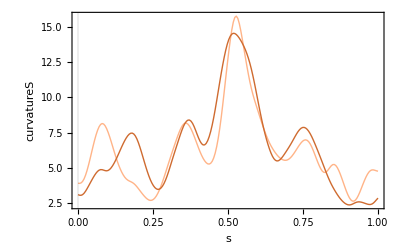
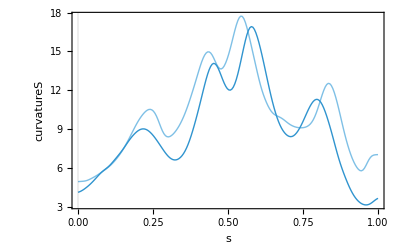
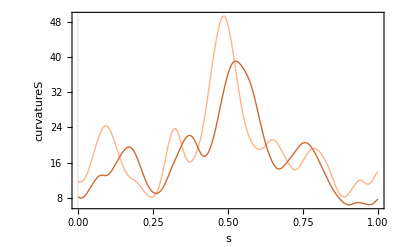
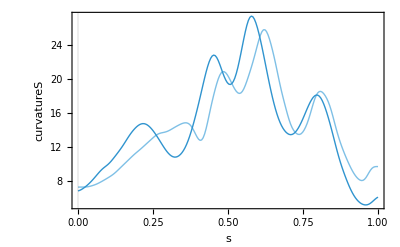
{{curvatureS-5,-Graphics-,-Graphics-},{curvatureS-nlen-5,-Graphics-,-Graphics-}}

```mathematica
{showMeanData[1][1][5],showMeanData[1][2][5]}
```

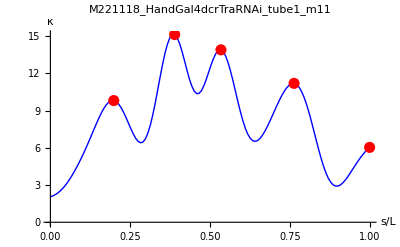

```mathematica
fileNumber = 7;
plotDeepPeaks[fileNumber]
```

```mathematica
(*The number of peaks*)
```

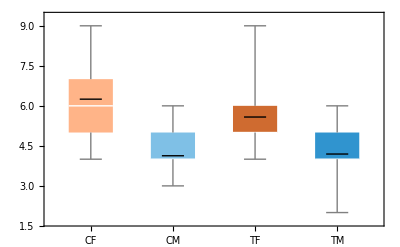
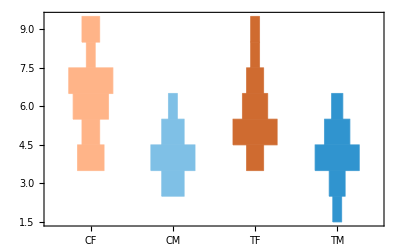
{-Graphics-,-Graphics-,0.053426,0.657099}

```mathematica
getNumPeak[experimentIndx_]:=(
rawControlFileDir= FileNameJoin[{NotebookDirectory[] , "Experiment" <> ToString[experimentIndx], "Control-centerlines"}];

rawTreatmentFileDir= FileNameJoin[{NotebookDirectory[] , "Experiment" <> ToString[experimentIndx], "Treatment-centerlines"}];

SetDirectory[rawControlFileDir];
controlNames = StringTake[FileNames[], {1, -5}];
controlNamesM= Select[controlNames, StringStartsQ[#, "M"]&];
controlNamesV= Select[controlNames, StringStartsQ[#, "V"]&];


SetDirectory[rawTreatmentFileDir];
treatNames = StringTake[FileNames[], {1, -5}];
treatNamesM= Select[treatNames, StringStartsQ[#, "M"]&];
treatNamesV= Select[treatNames, StringStartsQ[#, "V"]&];

controlIndsV = (Position[fileNames,# ]&/@controlNamesV)//Flatten;
treatIndsV = (Position[fileNames,# ]&/@treatNamesV)//Flatten;
controlIndsM= (Position[fileNames,# ]&/@controlNamesM)//Flatten;
treatIndsM = (Position[fileNames,# ]&/@treatNamesM)//Flatten;

allPeaks  = {getNumPeaks/@controlIndsV,getNumPeaks/@controlIndsM,getNumPeaks/@treatIndsV,getNumPeaks/@treatIndsM};

(*allPeaks = {getNumPeaks/@treatIndsV,getNumPeaks/@treatIndsM};*)
pf = LocationEquivalenceTest[allPeaks[[{1,3}]]];
pm = LocationEquivalenceTest[allPeaks[[{2,4}]]];

{
BoxWhiskerChart[allPeaks,"Mean", ChartStyle->groupColors[[-4;;]],ChartLabels->{"CF", "CM", "TF", "TM"}, LabelStyle->Directive[FontFamily->"Myriad Pro", Black, FontSize->16]],
DistributionChart[allPeaks,ChartStyle->groupColors[[-4;;]],ChartElementFunction->"HistogramDensity",ChartLabels->{"CF", "CM", "TF", "TM"}, LabelStyle->Directive[FontFamily->"Myriad Pro", Black, FontSize->16]], pf , pm}


)

getNumPeak[5]
```

```mathematica
(*run to plot all deep peaks*)
```

```mathematica
plotDeepPeaks/@Range[numFiles]
```

```mathematica
(*Tilt analysis, requires both cut types: midgut and full gut*)
```

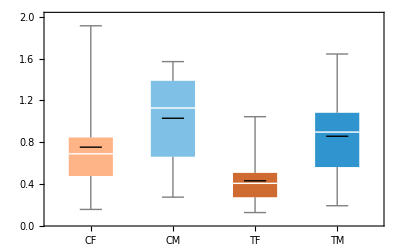
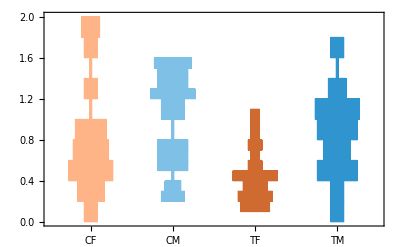
{-Graphics-,-Graphics-,0.00032099,0.0503589}

```mathematica
SetDirectory[resultDirectory];
changeDirectories[1]
majorAxes = getMajorAxis /@Range[numFiles];

changeDirectories[2]
majorAxesCut = getMajorAxis /@Range[numFiles];


tiltAngles = ArcCos[(majorAxes[[#]].majorAxesCut[[#]]&) /@Range[numFiles]];

getTilt[index_]:=tiltAngles[[index]];

getTiltAngle[experimentIndx_]:=(
rawControlFileDir= FileNameJoin[{NotebookDirectory[] , "Experiment" <> ToString[experimentIndx], "Control-centerlines"}];

rawTreatmentFileDir= FileNameJoin[{NotebookDirectory[] , "Experiment" <> ToString[experimentIndx], "Treatment-centerlines"}];

SetDirectory[rawControlFileDir];
controlNames = StringTake[FileNames[], {1, -5}];
controlNamesM= Select[controlNames, StringStartsQ[#, "M"]&];
controlNamesV= Select[controlNames, StringStartsQ[#, "V"]&];


SetDirectory[rawTreatmentFileDir];
treatNames = StringTake[FileNames[], {1, -5}];
treatNamesM= Select[treatNames, StringStartsQ[#, "M"]&];
treatNamesV= Select[treatNames, StringStartsQ[#, "V"]&];

controlIndsV = (Position[fileNames,# ]&/@controlNamesV)//Flatten;
treatIndsV = (Position[fileNames,# ]&/@treatNamesV)//Flatten;
controlIndsM= (Position[fileNames,# ]&/@controlNamesM)//Flatten;
treatIndsM = (Position[fileNames,# ]&/@treatNamesM)//Flatten;

allTilts  = {getTilt/@controlIndsV,getTilt/@controlIndsM,getTilt/@treatIndsV,getTilt/@treatIndsM};

(*allPeaks = {getNumPeaks/@treatIndsV,getNumPeaks/@treatIndsM};*)
pf = LocationEquivalenceTest[allTilts[[{1,3}]]];
pm = LocationEquivalenceTest[allTilts[[{2,4}]]];

{
BoxWhiskerChart[allTilts,"Mean", ChartStyle->groupColors[[-4;;]],ChartLabels->{"CF", "CM", "TF", "TM"}, LabelStyle->Directive[FontFamily->"Myriad Pro", Black, FontSize->16]],
DistributionChart[allTilts,ChartStyle->groupColors[[-4;;]],ChartElementFunction->"HistogramDensity",ChartLabels->{"CF", "CM", "TF", "TM"}, LabelStyle->Directive[FontFamily->"Myriad Pro", Black, FontSize->16]], pf , pm}

)



getTiltAngle[5]
```

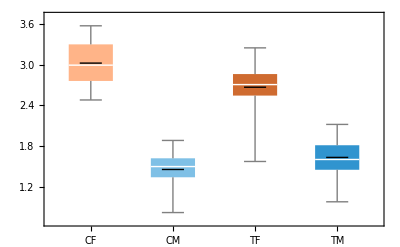
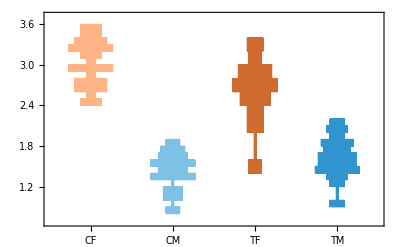
{-Graphics-,-Graphics-,0.0003436668009871389,0.00460571189652256}

```mathematica
plotLengthChange[experimentIndx_]:=(
rawControlFileDir= FileNameJoin[{NotebookDirectory[] , "Experiment" <> ToString[experimentIndx], "Control-centerlines"}];

rawTreatmentFileDir= FileNameJoin[{NotebookDirectory[] , "Experiment" <> ToString[experimentIndx], "Treatment-centerlines"}];

SetDirectory[rawControlFileDir];
controlNames = StringTake[FileNames[], {1, -5}];
controlNamesM= Select[controlNames, StringStartsQ[#, "M"]&];
controlNamesV= Select[controlNames, StringStartsQ[#, "V"]&];


SetDirectory[rawTreatmentFileDir];
treatNames = StringTake[FileNames[], {1, -5}];
treatNamesM= Select[treatNames, StringStartsQ[#, "M"]&];
treatNamesV= Select[treatNames, StringStartsQ[#, "V"]&];

controlIndsV = (Position[fileNames,# ]&/@controlNamesV)//Flatten;
treatIndsV = (Position[fileNames,# ]&/@treatNamesV)//Flatten;
controlIndsM= (Position[fileNames,# ]&/@controlNamesM)//Flatten;
treatIndsM = (Position[fileNames,# ]&/@treatNamesM)//Flatten;

allLengths  = {totalLength/@controlIndsV,totalLength/@controlIndsM,totalLength/@treatIndsV,totalLength/@treatIndsM};

(*allPeaks = {getNumPeaks/@treatIndsV,getNumPeaks/@treatIndsM};*)
pf = LocationEquivalenceTest[allLengths[[{1,3}]]];
pm = LocationEquivalenceTest[allLengths[[{2,4}]]];

{
BoxWhiskerChart[allLengths,"Mean", ChartStyle->groupColors[[-4;;]],ChartLabels->{"CF", "CM", "TF", "TM"}, LabelStyle->Directive[FontFamily->"Myriad Pro", Black, FontSize->16]],
DistributionChart[allLengths,ChartStyle->groupColors[[-4;;]],ChartElementFunction->"HistogramDensity",ChartLabels->{"CF", "CM", "TF", "TM"}, LabelStyle->Directive[FontFamily->"Myriad Pro", Black, FontSize->16]], pf , pm}


)

plotLengthChange [5]
```

```mathematica
(*Plotting the mds results *)
```

```mathematica
ClearAll["Global`*"]

op = 0.2;

dataNames = {"curvatureS","angle","height","torsionS","radiusS"};
registrationNames = {"-fixed","-aligned"};
normalizationNames={"-","-nlen-","-nrad-"};

resultDirectory = FileNameJoin[{NotebookDirectory[], "RunResults"}];


groupColors = {Red, Purple, ResourceFunction["HexToColor"]["#FFB488"],ResourceFunction["HexToColor"]["#7FC0E6"],ResourceFunction["HexToColor"]["#CF6B30"], ResourceFunction["HexToColor"]["#3094CF"]};
vcColor = groupColors[[3]];mcColor = groupColors[[4]];
vtColor = groupColors[[5]];mtColor = groupColors[[6]];


ellipsoid[points_]:=(
mean = Mean[points]; cov = Covariance[points];
nSigma = 2; 
confidence = {0.68, 0.95, 99.7}[[nSigma]];

Ellipsoid[mean,cov Quantile[ChiSquareDistribution[3],confidence]]
)

(*axes[points_]:=(
mean = Mean[points]; cov = Covariance[points];


vecs =Eigenvectors[cov]; vals =Sqrt[Quantile[ChiSquareDistribution[3],confidence]Eigenvalues[cov]];

Line[{(mean- vals[[#]]*vecs[[#]]),(mean+vals[[#]]*vecs[[#]])}&/@Range[3]]
)*)

mdsAnalysis[dataIndex_:1,regIndex_:1][ normIndex_,experimentIndx_]:= (

dataName = dataNames[[dataIndex]];
registrationName = registrationNames[[regIndex]];
normalizationName = normalizationNames[[normIndex]];



controlDir  = FileNameJoin[{NotebookDirectory[], "Experiment" <>ToString[experimentIndx], "Control-centerlines"}];
SetDirectory[controlDir];
controlNames = StringTake[FileNames[], {1, -5}];

treatmentDir = FileNameJoin[{NotebookDirectory[], "Experiment" <>ToString[experimentIndx], "Treatment-centerlines"}];
SetDirectory[treatmentDir];
treatmentNames = StringTake[FileNames[], {1, -5}];


numVirgConts= Total[Boole[StringTake[#,1]=="V"&/@controlNames]];
numMaleConts= Total[Boole[StringTake[#,1]=="M"&/@controlNames]];

numVirgTreats= Total[Boole[StringTake[#,1]=="V"&/@treatmentNames]];
numMaleTreats= Total[Boole[StringTake[#,1]=="M"&/@treatmentNames]];

numControls = numVirgConts + numMaleConts;
numTreatments = numVirgTreats+ numMaleTreats;


numFiles =(* numFemales + numVirgins + numMales +*)numControls + numTreatments;


SetDirectory[resultDirectory];


(*deleteInds = {{70}};*)


distanceMatrix = Import[dataName<>registrationName<>normalizationName <>"exp-"<>ToString[experimentIndx]<>"-distMat.csv"]; 


(*distanceMatrix =Delete[Delete[ distanceMatrix,deleteInds]//Transpose,deleteInds]//Transpose;
Export[dataName <>"dist_mat.csv", distanceMatrix]
*)

nDistMat = distanceMatrix/Max[distanceMatrix];
labelBoundaries  = {1, numControls +1  ,numFiles};

mdsPoints = Import[dataName<>registrationName<>normalizationName <>"exp-"<>ToString[experimentIndx]<>"-mdsCoords.csv"]//N;


vcPoints = mdsPoints[[;; numVirgConts]];
mcPoints = mdsPoints[[ numVirgConts + 1;; numControls]];
vtPoints = mdsPoints[[numControls+ 1;;  numControls +numVirgTreats ]];
mtPoints = mdsPoints[[ numControls +numVirgTreats + 1;;]];


(*vTTest = TTest[{vcPoints,vtPoints} ,0];
mTTest =TTest[{mcPoints,mtPoints} ,0];*)

vLTest = LocationTest[{vcPoints,vtPoints}];
mLTest = LocationTest[{mcPoints,mtPoints} ];

(*Print[ LocationTest[{vcPoints,vtPoints}, Automatic, {"TestDataTable", All}]];
Print[ LocationTest[{mcPoints,mtPoints}, Automatic, {"TestDataTable", All}]];*)


(*vcRegion = BoundingRegion[vcPoints, "MinConvexPolyhedron"];*)
vcRegion = ellipsoid[vcPoints];
vcPlot = Graphics3D[{vcColor, Point[vcPoints], Opacity[op],vcRegion}];


(*mcRegion = BoundingRegion[mcPoints, "MinConvexPolyhedron"];*)
mcRegion = ellipsoid[mcPoints]; mcAxes = axes[mcPoints];
mcPlot = Graphics3D[{mcColor, Point[mcPoints], Opacity[op],mcRegion}];


(*vtRegion = BoundingRegion[vtPoints, "MinConvexPolyhedron"];*)
vtRegion = ellipsoid[vtPoints];
vtPlot = Graphics3D[{vtColor, Point[vtPoints], Opacity[op],vtRegion}];

(*mtRegion = BoundingRegion[mtPoints, "MinConvexPolyhedron"];*)
mtRegion = ellipsoid[mtPoints];
mtPlot = Graphics3D[{mtColor, Point[mtPoints], Opacity[op],mtRegion}];


regCentroids = RegionCentroid/@{vcRegion, vtRegion,mcRegion, mtRegion};
centroidDistances = DistanceMatrix[regCentroids]//MatrixForm;

centroidPlot  = Graphics3D[{PointSize[0.02],Lighter[vtColor], Point[regCentroids[[1]]],Lighter[mtColor],Point[regCentroids[[3]]],PointSize[0.035],vtColor, Point[regCentroids[[2]]],Arrow[{regCentroids[[1]],regCentroids[[2]]}],mtColor, Point[regCentroids[[4]]], Arrow[{regCentroids[[3]],regCentroids[[4]]}]}];



vp = {1.677914282467398,-0.2570664029822958,0.3442681006855887};
expFig = Show[mcPlot, vcPlot, centroidPlot, Axes->True, AxesLabel->{"μ_1", "μ_2", "μ_3"}];

{expFig, {vLTest,mLTest} }

)

1
```

1

```mathematica
expInd =5;
{mdsAnalysis[1,1][1, expInd], mdsAnalysis[1,1][2, expInd]}
{mdsAnalysis[1,2][1,expInd], mdsAnalysis[1,2][2, expInd]}
```

{{-Graphics3D-,{0.271332,0.000130627}},{-Graphics3D-,{0.00254971,0.0577352}}}

{{-Graphics3D-,{0.0608487,0.000217634}},{-Graphics3D-,{0.000757886,0.300807}}}

```mathematica
mdsAnalysis[1,1][1,expInd]
 mdsAnalysis[1,2][1,expInd]
numVirgConts
numMaleConts
```

{-Graphics3D-,{0.271332,0.000130627}}

{-Graphics3D-,{0.0608487,0.000217634}}

28

31